```mathematica
$Assumptions={n∈Integers}
```

{n∈ℤ}

```mathematica
Solve[b+d==π/n(1-Cos[n π])&&b 3^n+d 3^-n==π/n(Cos[n π]-1),{b,d}]//FullSimplify
```

{{b→((-1+(-1)^n) π)/((-1+3^n) n),d→-(3^n (-1+(-1)^n) π)/((-1+3^n) n)}}

```mathematica
(∫_0^(Pi/2) (1+2/Pi θ)Cos[n θ]ⅆθ)/(∫_0^(Pi/2) (Cos[n θ])^2ⅆθ)//FullSimplify
```

(8 (-1+Cos[(n π)/2]+n π Sin[(n π)/2]))/(n^2 π^2)

```mathematica
(∫_0^(Pi/2) (1+2/Pi θ)Sin[n θ]ⅆθ)/(∫_0^(Pi/2) (Sin[n θ])^2ⅆθ)//FullSimplify
```

(4 n π-8 n π Cos[(n π)/2]+8 Sin[(n π)/2])/(n^2 π^2)

```mathematica
uwedge[r_,θ_]:=1+2/Pi θ
```

```mathematica
Plot3D[uwedge[Norm[{x,y}],ArcTan[x,y]],{x,0,2},{y,0,2},RegionFunction->Function[{x, y}, x^2 + y^2 ≤4]]
```

-Graphics3D-

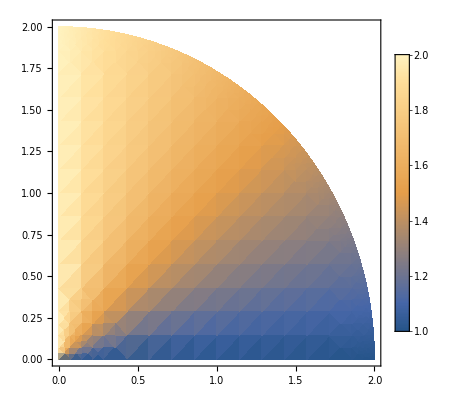

```mathematica
DensityPlot[uwedge[Norm[{x,y}],ArcTan[x,y]],{x,0,2},{y,0,2},RegionFunction->Function[{x, y}, x^2 + y^2 ≤4],PlotLegends->Automatic]
```